```mathematica
ClearAll["Global`*"]
```

```mathematica
α=5;
a=3.543543;
V[x_]:=1/2(a^2 Abs[x]^(2α-2)-a(α-1)Abs[x]^(α-2))
NDEigensystem[{-1/2 Cos[x]^2D[Cos[x]^2f'[x],x]+V[Tan[x]]f[x],DirichletCondition[f[x]==0,True]},f[x],{x,-Pi/2,Pi/2},3(*,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}},"VectorNormalization"->Function[{values,vectors,stiffness,damping},s=stiffness;
d=damping;
norm=vectors/(Diagonal[vectors.damping.ConjugateTranspose[vectors]]^(1/2)*NIntegrate[2/Cos[x]^2,{x,0,Pi/2}])]}*)]
```

```mathematica
<<MaTeX`
```

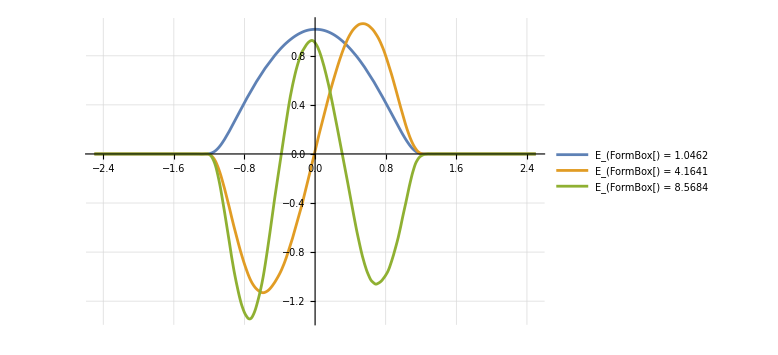

```mathematica
Module[{V,egl,regv,egv,a=1,α=20,k=3,s=1,ss},
V[x_]:=1/2(a^2 Abs[x]^(2α-2)+s a(α-1)Abs[x]^(α-2));
ss=If[s==1,"+","-"];
{egl,regv}=NDEigensystem[{-1/2 Cos[x]^2D[Cos[x]^2f'[x],x]+V[Tan[x]]f[x],DirichletCondition[f[x]==0,True]},f[x],{x,-Pi/2,Pi/2},n,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}];
lbl[k_]:=StringForm["E_(``, ``) = ``",k,ss,NumberForm[egl[[k]],{10,4}]];
egv=Table[regv[[i]]/Sign[regv[[i]]/.x->.1](*/Sqrt[NIntegrate[2 regv[[i]]^2/Cos[x]^2,{x,0,Pi/2-.2}]]*),{i,n}];
Plot[egv[[;;k]]/.x->ArcTan[x]//Evaluate,{x,-2.5,2.5},
PlotRange->Automatic,
PlotLegends->Placed[LineLegend[Automatic,Style[#,FontFamily->"Latin Modern Roman 12",12]&/@Table[lbl[k],{k,n}],LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{.87,.85}],
ImageSize->Large,
GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashing[{0.01,0.01}]],
Frame->Automatic,FrameLabel->"First 3 eigenfunctions of"MaTeX["V_"<>ss],BaseStyle->{FontFamily->"Arial",FontSize->12}]
]
```

```mathematica
(*Run the code to dynamically solve and plot energies and wave functions.
Caveat: numericals are unstable in some choice of parameters.*)
n=5;
Manipulate[Module[{V,egl,regv,egv},
V[x_]:=1/2(a^2 Abs[x]^(2α-2)+s a(α-1)Abs[x]^(α-2));
{egl,regv}=NDEigensystem[{-1/2 Cos[x]^2D[Cos[x]^2f'[x],x]+V[Tan[x]]f[x],DirichletCondition[f[x]==0,True]},f[x],{x,-Pi/2,Pi/2},n,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}}}];
lbl[k_]:=StringForm["E_(``, ``) = ``",k,If[s==1,"+","-"],NumberForm[egl[[k]],{10,6}]];
egv=Table[regv[[i]]/Sign[regv[[i]]/.x->.1](*/Sqrt[NIntegrate[2 regv[[i]]^2/Cos[x]^2,{x,0,Pi/2-.2}]]*),{i,n}];
If[display,Plot[egv[[;;k]]/.x->ArcTan[x]//Evaluate,{x,-3,3},
PlotRange->1.2,
PlotLegends->Table[lbl[k],{k,n}],
ImageSize->Large],
Plot[egv[[k]]/.x->ArcTan[x]//Evaluate,{x,-5,5},PlotRange->1.45,PlotLabel->lbl[k],
ImageSize->Large,Filling->Axis,GridLines->Automatic
]]
]
,{α,1,5},{{a,1},0,5},{s,{1,-1}},{k,Range[n]},{display,{True->"All",False->"Individual"}}
]
```